```mathematica
Quit[];
```

```mathematica
ScalarF0[m_,s_]:=2-2Log[m]-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))];
PropagatorScalar[s_,M_,m_,c_,MΓ_]:=1/(s-M^2+c×ScalarF0[m,s]+ⅈ×MΓ);
```

```mathematica
data[m_,c_,MΓ_]:=Table[{p,Abs[PropagatorScalar[p^2,1,m,c,MΓ]]^2},{p,0.1,1.9,0.01}];
nlm[m_,c_,MΓ_]:=NonlinearModelFit[data[m,c,MΓ],C/((x^2-A)^2+B),{{A,1},{B,MΓ^2},{C,1}},x];
```

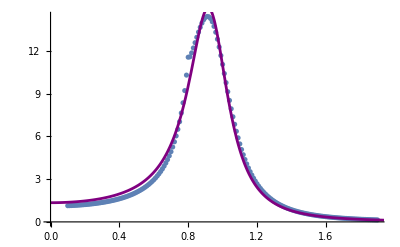

```mathematica
Show[ListPlot[data[0.399,0.04,0.2]],Plot[nlm[0.399,0.04,0.2][p],{p,0,2},PlotRange->Full,PlotStyle->Purple]]
```

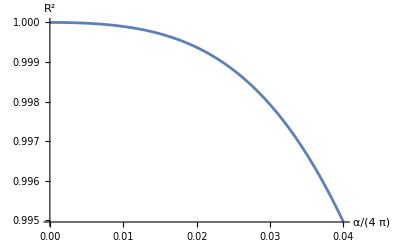

```mathematica
Plot[nlm[0.399,c,0.2]["RSquared"],{c,0,0.04},AxesLabel->{α/(4π),R^2}]
```

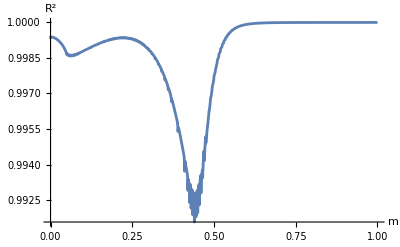

```mathematica
Plot[nlm[m,0.04,0.2]["RSquared"],{m,0,1},PlotRange->Full,AxesLabel->{m,R^2}]
```

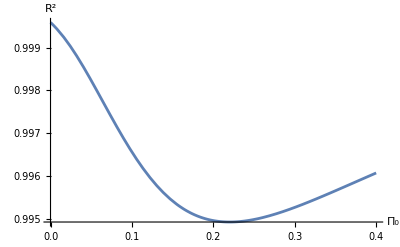

```mathematica
Plot[nlm[0.399,0.04,MΓ]["RSquared"],{MΓ,0,0.4},AxesLabel->{Subscript[Π, 0],R^2}]
(*A bit missleading*)
```